### Set Options

Automating good looking plots

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

```mathematica
SetOptions[ ListContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ ListDensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

```mathematica
SetOptions[ ContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ DensityPlot,Frame-> True,LabelStyle->{FontFamily->"CMU Serif",FontSize->24,Black},ImageSize->Medium];
```

### Parameters

Lattice vectors, and basis vectors

```mathematica
a1 = {1,0};a2 ={0,1};τA = {1/2,0};τB = {0,0}; τC = {0,1/2};τvec = {τA,τB, τC};
```

Reciprocal lattice vectors

```mathematica
LatMat = {a1,a2}; 
ReciLatMat = 2π Inverse[LatMat]†;
b1 = ReciLatMat[[1]] ;b2 = ReciLatMat[[2]];
```

```mathematica
δf=N[1/(2√2)];
```

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
rSpan[range_]:=N[Flatten[Table[i*a1+j*a2,{i,-range,range},{j,-range,range}],1]];
```

```mathematica
inp[a_,b_]:= Conjugate[a].b;
```

We will play around with k-range and range to check for convergence

### Bloch Hamiltonian

```mathematica
akp[δ_,k_] := N[(1+δ)/2 + (1-δ)/2 Exp[I k]];akm[δ_,k_] := N[(1+δ)/2 -  (1-δ)/2 Exp[I k]];
```

```mathematica
(*akp[δ_,k_]:=N[Cos[k/2] + I δ Sin[k/2]]; akm[δ_,k_]:=N[δ Cos[k/2] - I  Sin[k/2]]*)
```

```mathematica
Clear[hamLieb];hamLieb[λ_,δ_,k_] := hamLieb[λ,δ,k] = Module[ {kx =k[[1]], ky = k[[2]],δx = δ[[1]], δy = δ[[2]]},{{0,0, - akp[δx,-kx], λ  akm[δx,-kx],0,0},{0,0, -λ akm[δx,-kx], - akp[δx,-kx],0,0},{-akp[δx,kx],-λ akm[δx,kx],0,0,-akp[δy,ky], I λ akm[δy,ky]},{λ akm[δx,kx], - akp[δx,kx],0,0,I λ akm[δy,ky], - akp[δy,ky]},{0,0, - akp[δy,-ky], -I λ  akm[δy,-ky],0,0},{0,0, -I λ akm[δy,-ky], - akp[δy,-ky],0,0}}];
```

```mathematica
Block[ {λ=RandomReal[],δ=RandomReal[1,2],k=RandomReal[2π,2]},hamLieb[λ,δ,k]]//MatrixForm
```

(0 | 0 | -0.820314-0.372323 ⅈ | 0.0411858-0.0671044 ⅈ | 0 | 0
0 | 0 | -0.0411858+0.0671044 ⅈ | -0.820314-0.372323 ⅈ | 0 | 0
-0.820314+0.372323 ⅈ | -0.0411858-0.0671044 ⅈ | 0 | 0 | -0.555677+0.37774 ⅈ | -0.0680807+0.122353 ⅈ
0.0411858+0.0671044 ⅈ | -0.820314+0.372323 ⅈ | 0 | 0 | -0.0680807+0.122353 ⅈ | -0.555677+0.37774 ⅈ
0 | 0 | -0.555677-0.37774 ⅈ | -0.0680807-0.122353 ⅈ | 0 | 0
0 | 0 | -0.0680807-0.122353 ⅈ | -0.555677-0.37774 ⅈ | 0 | 0)

```mathematica
Block[ {λ=RandomReal[],δ=RandomReal[1,2],k=RandomReal[2π,2]},HermitianMatrixQ[ hamLieb[λ,δ,k]]]
```

True

```mathematica
Clear[EnerLieb];EnerLieb[λ_,δ_,k_] := EnerLieb[λ,δ,k]= Chop[  N[Sort[Eigenvalues[hamLieb[λ,δ,k] ]]] ];
Clear[ULiebG2];ULiebG2[λ_,δ_,k_] :=ULiebG2[λ,δ,k]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[ hamLieb[λ,δ,k] ] ] ,First ] ][[2]] ] ] ] ;
```

#### Plot Band Structure

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
PlotDispData[λ_,δ_] := Table[ EnerLieb[λ,δ,k]  ,{k,kCut} ];
```

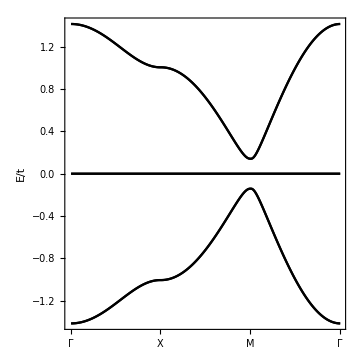

```mathematica
Block[ {λ=0.0,δ={0.1,0.1}},ListPlot[Table[ PlotDispData[λ,δ][[All,i]],{i,1,6}],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Analytic Flat-band Wavefunction

```mathematica
mat = {{0,0,a, b, 0,0},{0,0,-b, a,0,0},{ac, -bc,0,0,x,I y},{bc, ac,0,0,I y,x},{0,0,xc, -I yc,0,0},{0,0,-I yc, xc,0,0}};
```

```mathematica
vec1 = {(-bc x - I ac y)/(ac^2+bc^2),(-ac x + I bc y)/(ac^2+bc^2) ,0,0,0,1};
```

```mathematica
vec2 = {0,-1,0,0,(-x bc - I y ac)/(x^2+y^2),(-I(-y bc + I x ac))/(x^2+y^2) };
```

```mathematica
mat.(vec1+vec2)//MatrixForm//Simplify
```

(0
0
0
0
0
0)

```mathematica
(*Eigensystem[mat][[2]][[1]]*)
```

```mathematica
(*Eigensystem[mat][[2]][[2]]*)
```

```mathematica
Clear[waveF];waveF[λ_,δ_,k_] := waveF[λ,δ,k]=Normalize[ Module[{a = - akp[δ[[1]],-k[[1]]],b= λ  akm[δ[[1]],-k[[1]]],x = -akp[δ[[2]],k[[2]]],y= λ akm[δ[[2]],k[[2]]]}, { - Conjugate[b] x - I Conjugate[a] y,   - Conjugate[a] x + I Conjugate[b] y,0,0,0, Conjugate[b]^2+ Conjugate[a]^2}]];
```

```mathematica
Clear[waveF2];waveF2[λ_,δ_,k_] := waveF2[λ,δ,k]=Normalize[ Module[{a = - akp[δ[[1]],-k[[1]]],b= λ  akm[δ[[1]],-k[[1]]],x = -akp[δ[[2]],k[[2]]],y= λ akm[δ[[2]],k[[2]]]}, { 0,-x^2-y^2, 0,0,- x Conjugate[b] - I y Conjugate[a], I y Conjugate[b]+ x Conjugate[a] }]];
```

```mathematica
Block[ {λ=RandomReal[],δ=RandomReal[1,2],k=RandomReal[2π,2]}, hamLieb[λ,δ,k].waveF[λ,δ,k]]//MatrixForm//Chop
```

(0
0
0
0
0
0)

```mathematica
Block[ {λ=RandomReal[],δ=RandomReal[1,2],k=RandomReal[2π,2]}, hamLieb[λ,δ,k].waveF2[λ,δ,k]]//MatrixForm//Chop
```

(0
0
0
0
0
0)

```mathematica
Block[ {λ=0.6,δ={0.5,0.0},k=RandomReal[2π,2]}, hamLieb[λ,δ,k].(Normalize[waveF[λ,δ,k]+waveF2[λ,δ,k]])]//MatrixForm//Chop
```

(0
0
0
0
0
0)

```mathematica
TRO = KroneckerProduct[  IdentityMatrix[3],I  PauliMatrix[2]];
```

```mathematica
Block[ {λ=0.6,δ={0.5,0.0},k=RandomReal[2π,2]}, hamLieb[λ,δ,k].(TRO.Conjugate[Normalize[waveF[λ,δ,-k]+waveF2[λ,δ,-k]]])]//MatrixForm//Chop
```

(0
0
0
0
0
0)

### Wannier Functions

```mathematica
Clear[Psi];Psi[λ_,δ_,k_,band_]:= Psi[λ,δ,k,band]=Module[ {vec =Normalize[waveF[λ,δ,k]+ waveF2[λ,δ,k]], veck =Normalize[waveF[λ,δ,-k]+ waveF2[λ,δ,-k]]},  If[band==1, vec,TRO.Conjugate[veck] ]];
```

```mathematica
Psi[RandomReal[],RandomReal[1,2],RandomReal[2π,2],2]//MatrixForm
```

(-0.52648-0.305972 ⅈ
0.175574+0.0879716 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.626178-0.39227 ⅈ
0.188937+0.0946671 ⅈ)

```mathematica
Clear[WanFuPsi];WanFuPsi[λ_,δ_,r_,krange_,band_] := WanFuPsi[λ,δ,r,krange,band]=1/Length[kSpan[krange]] Sum[Exp[-I k.r]  Psi[λ,δ,k,band] ,{k,kSpan[krange]}]
```

now it’s amplitude

```mathematica
Clear[WFAmpPsi];WFAmpPsi[λ_,δ_,r_,krange_,band_] := WFAmpPsi[λ,δ,r,krange,band] =  Norm[WanFuPsi[λ,δ,r,krange,band]]^2;
```

```mathematica
Block[ {λ=0.5,δ={0.5,0.5},krange=50,band=1,r=τB}, WanFuPsi[λ,δ,r,krange,band]]//MatrixForm
```

(0.153645+0.144832 ⅈ
-0.629247+0.0804683 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.144832+0.153645 ⅈ
0.629247+0.0804683 ⅈ)

```mathematica
Block[ {λ=0.5,δ={0.5,0.5},krange=50,band=1},WFAmpPsi[λ,δ,{0,0},krange,band ]]//MatrixForm
```

0.894021

```mathematica
Clear[OmegaPsi];OmegaPsi[ λ_,δ_,range_,krange_,band_] := OmegaPsi[λ,δ,range,krange,band] =  Sum[ Norm[r]^2 WFAmpPsi[λ,δ,r,krange,band] ,{r,rSpan[range]}]- Norm[Sum[r  WFAmpPsi[λ,δ,r,krange,band] ,{r,rSpan[range]}]]^2;
```

#### Wannier Checks

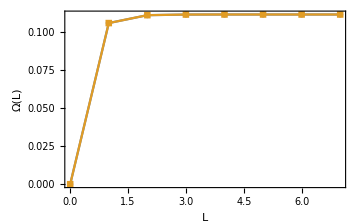

```mathematica
Block[ {λ=0.5,δ={0.5,0.5},krange=50,band=1},DiscretePlot[ {OmegaPsi[λ,δ,range,krange,1],OmegaPsi[λ,δ,range,krange,2]}, {range,0,7}, FrameLabel->{"L","Ω(L)"},PlotMarkers->Automatic] ]
```

Not much difference between spatial structure of 1 and 2

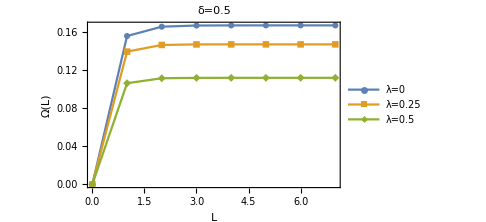

```mathematica
Block[ {λ=0.25,δ={0.5,0.5},krange=50,band=1},DiscretePlot[ {OmegaPsi[0.0,δ,range,krange,1],OmegaPsi[λ,δ,range,krange,1],OmegaPsi[2 λ,δ,range,krange,1]}, {range,0,7}, FrameLabel->{"L","Ω(L)"},PlotMarkers->Automatic,PlotLegends->{"λ=0","λ=0.25","λ=0.5"},PlotLabel->"δ=0.5"] ]
```

Now let us look at structure of Wannier Function

```mathematica
Block[ {λ=0.25,δ={0.5,0.5},krange=50,r={0,0},band=1},WanFuPsi[λ,δ,r,krange,band]]//MatrixForm//Chop
```

(0.0915486+0.0834593 ⅈ
-0.643612+0.0244047 ⅈ
0
0
0.0834593+0.0915486 ⅈ
0.643612+0.0244047 ⅈ)

```mathematica
Block[ {λ=0.25,δ={0.5,0.5},krange=50,r={0,0},band=2},WanFuPsi[λ,δ,r,krange,band]]//MatrixForm//Chop
```

(-0.643612-0.0244047 ⅈ
-0.0915486+0.0834593 ⅈ
0
0
0.643612-0.0244047 ⅈ
-0.0834593+0.0915486 ⅈ)

### Projected Interactions

```mathematica
Clear[ProjIntNN];ProjIntNN[λ_,δ_,r_,l_,krange_,range_]:=ProjIntNN[λ,δ,r,l,krange,range] = Module[ {l1 = l[[1]], l2 = l[[2]], l3 = l[[3]], l4 = l[[4]]}, Sum[Sum[ Conjugate[WanFuPsi[λ,δ,-rS,krange,l1][[α]]]WanFuPsi[λ,δ,-rS,krange,l2][[α]] Conjugate[WanFuPsi[λ,δ,r-rS,krange,l3][[α+1]]]WanFuPsi[λ,δ,r-rS,krange,l4][[α+1]],{α,1,6,2}],{rS,rSpan[range]}]]
```

```mathematica
Clear[ProjIntSF];ProjIntSF[λ_,δ_,r_,l_,krange_,range_]:=ProjIntSF[λ,δ,r,l,krange,range] = Module[ {l1 = l[[1]], l2 = l[[2]], l3 = l[[3]], l4 = l[[4]]}, Sum[Sum[ Conjugate[WanFuPsi[λ,δ,-rS,krange,l1][[α]]]WanFuPsi[λ,δ,-rS,krange,l2][[α+1]] WanFuPsi[λ,δ,r-rS,krange,l3][[α]]Conjugate[WanFuPsi[λ,δ,r-rS,krange,l4][[α+1]]],{α,1,6,2}],{rS,rSpan[range]}]]
```

```mathematica
Clear[ProjIntPH];ProjIntPH[λ_,δ_,r_,l_,krange_,range_]:=ProjIntPH[λ,δ,r,l,krange,range] = Module[ {l1 = l[[1]], l2 = l[[2]], l3 = l[[3]], l4 = l[[4]]}, Sum[Sum[ Conjugate[WanFuPsi[λ,δ,-rS,krange,l1][[α]]]Conjugate[WanFuPsi[λ,δ,-rS,krange,l2][[α+1]] ]WanFuPsi[λ,δ,r-rS,krange,l3][[α+1]]WanFuPsi[λ,δ,r-rS,krange,l4][[α]],{α,1,6,2}],{rS,rSpan[range]}]]
```

#### On-site Hubbard

```mathematica
Block[ {λ=0.0,δ={0.5,0.5}, r={0,0}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntNN[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 2 | 0
1 | 1 | 2 | 1 | 0
1 | 1 | 2 | 2 | 0
1 | 2 | 1 | 1 | 0
1 | 2 | 1 | 2 | 0
1 | 2 | 2 | 1 | 0
1 | 2 | 2 | 2 | 0
2 | 1 | 1 | 1 | 0
2 | 1 | 1 | 2 | 0
2 | 1 | 2 | 1 | 0
2 | 1 | 2 | 2 | 0
2 | 2 | 1 | 1 | 0.361899
2 | 2 | 1 | 2 | 0
2 | 2 | 2 | 1 | 0
2 | 2 | 2 | 2 | 0)

#### Nearest Neighbor

```mathematica
λ=0.2;
```

```mathematica
Block[ {δ={0.5,0.5}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntNN[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.00074975
1 | 1 | 1 | 2 | 0.0000282629+0.0000810675 ⅈ
1 | 1 | 2 | 1 | 0.0000282629-0.0000810675 ⅈ
1 | 1 | 2 | 2 | 0.0000350069
1 | 2 | 1 | 1 | -0.00202223+0.00146729 ⅈ
1 | 2 | 1 | 2 | -0.000475823+0.0000687614 ⅈ
1 | 2 | 2 | 1 | -0.00014371+0.000487966 ⅈ
1 | 2 | 2 | 2 | 0.0000152577-0.0000406503 ⅈ
2 | 1 | 1 | 1 | -0.00202223-0.00146729 ⅈ
2 | 1 | 1 | 2 | -0.00014371-0.000487966 ⅈ
2 | 1 | 2 | 1 | -0.000475823-0.0000687614 ⅈ
2 | 1 | 2 | 2 | 0.0000152577+0.0000406503 ⅈ
2 | 2 | 1 | 1 | 0.027912
2 | 2 | 1 | 2 | 0.00204922+0.00233598 ⅈ
2 | 2 | 2 | 1 | 0.00204922-0.00233598 ⅈ
2 | 2 | 2 | 2 | 0.001347)

```mathematica
Block[ {δ={0.5,0.2}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntNN[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.000836984
1 | 1 | 1 | 2 | -7.0433×10^-6+0.0000467884 ⅈ
1 | 1 | 2 | 1 | -7.0433×10^-6-0.0000467884 ⅈ
1 | 1 | 2 | 2 | 0.0000217922
1 | 2 | 1 | 1 | -0.00140838+0.000248645 ⅈ
1 | 2 | 1 | 2 | -0.000240876+0.00016821 ⅈ
1 | 2 | 2 | 1 | -0.000165389+0.000343656 ⅈ
1 | 2 | 2 | 2 | 0.0000595931-0.000118942 ⅈ
2 | 1 | 1 | 1 | -0.00140838-0.000248645 ⅈ
2 | 1 | 1 | 2 | -0.000165389-0.000343656 ⅈ
2 | 1 | 2 | 1 | -0.000240876-0.00016821 ⅈ
2 | 1 | 2 | 2 | 0.0000595931+0.000118942 ⅈ
2 | 2 | 1 | 1 | 0.056911
2 | 2 | 1 | 2 | 0.00103363+0.00217027 ⅈ
2 | 2 | 2 | 1 | 0.00103363-0.00217027 ⅈ
2 | 2 | 2 | 2 | 0.00166441)

```mathematica
Block[ {δ={0.5,0.2}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntSF[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.000164701-0.000350599 ⅈ
1 | 1 | 1 | 2 | 0.0000691506-0.000110677 ⅈ
1 | 1 | 2 | 1 | -0.00125397+0.000381816 ⅈ
1 | 1 | 2 | 2 | -0.000164701+0.000350599 ⅈ
1 | 2 | 1 | 1 | -0.0000321467+0.0000187838 ⅈ
1 | 2 | 1 | 2 | 6.64395×10^-6+0.0000132593 ⅈ
1 | 2 | 2 | 1 | 0.000252444+0.000755318 ⅈ
1 | 2 | 2 | 2 | 0.0000321467-0.0000187838 ⅈ
2 | 1 | 1 | 1 | -0.00080641+0.00228371 ⅈ
2 | 1 | 1 | 2 | 0.00130328+0.000508249 ⅈ
2 | 1 | 2 | 1 | 0.0568661-0.00120367 ⅈ
2 | 1 | 2 | 2 | 0.00080641-0.00228371 ⅈ
2 | 2 | 1 | 1 | -0.000164701+0.000350599 ⅈ
2 | 2 | 1 | 2 | -0.0000691506+0.000110677 ⅈ
2 | 2 | 2 | 1 | 0.00125397-0.000381816 ⅈ
2 | 2 | 2 | 2 | 0.000164701-0.000350599 ⅈ)

```mathematica
Block[ {δ={0.5,0.2}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntPH[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.000165389-0.000343656 ⅈ
1 | 1 | 1 | 2 | -0.00140838+0.000248645 ⅈ
1 | 1 | 2 | 1 | -0.0000595931+0.000118942 ⅈ
1 | 1 | 2 | 2 | -0.000240876+0.00016821 ⅈ
1 | 2 | 1 | 1 | -7.0433×10^-6-0.0000467884 ⅈ
1 | 2 | 1 | 2 | -0.000836984
1 | 2 | 2 | 1 | 0.0000217922
1 | 2 | 2 | 2 | 7.0433×10^-6-0.0000467884 ⅈ
2 | 1 | 1 | 1 | -0.00103363+0.00217027 ⅈ
2 | 1 | 1 | 2 | 0.056911
2 | 1 | 2 | 1 | -0.00166441
2 | 1 | 2 | 2 | 0.00103363+0.00217027 ⅈ
2 | 2 | 1 | 1 | -0.000240876-0.00016821 ⅈ
2 | 2 | 1 | 2 | 0.00140838+0.000248645 ⅈ
2 | 2 | 2 | 1 | 0.0000595931+0.000118942 ⅈ
2 | 2 | 2 | 2 | 0.000165389+0.000343656 ⅈ)

#### Fermionic det

```mathematica
FDet[l_]:= Det[ {{l[[1]], l[[2]], l[[3]], l[[4]]},{l[[2]], l[[3]], l[[4]], l[[1]]},{l[[3]], l[[4]], l[[1]], l[[2]]},{l[[4]], l[[1]], l[[2]], l[[3]]}}];
```

```mathematica
Flatten[Table[ {l1,l2,l3,l4,Sign[FDet[{l1,l2,l3,l4}]]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 2 | 1
1 | 1 | 2 | 1 | -1
1 | 1 | 2 | 2 | 0
1 | 2 | 1 | 1 | 1
1 | 2 | 1 | 2 | 0
1 | 2 | 2 | 1 | 0
1 | 2 | 2 | 2 | 1
2 | 1 | 1 | 1 | -1
2 | 1 | 1 | 2 | 0
2 | 1 | 2 | 1 | 0
2 | 1 | 2 | 2 | -1
2 | 2 | 1 | 1 | 0
2 | 2 | 1 | 2 | 1
2 | 2 | 2 | 1 | -1
2 | 2 | 2 | 2 | 0)

#### Detail layout

Density-Density channel

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={1,0}, krange=50,range=3}, {ProjIntNN[λ,δ,r,{1,1,1,1},krange,range],ProjIntNN[λ,δ,r,{2,2,2,2},krange,range],ProjIntNN[λ,δ,r,{1,1,2,2},krange,range],ProjIntNN[λ,δ,r,{2,2,1,1},krange,range]}]//MatrixForm//Chop
```

(0.00074975
0.001347
0.0000350069
0.027912)

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={-1,0}, krange=50,range=3}, {ProjIntNN[λ,δ,r,{1,1,1,1},krange,range],ProjIntNN[λ,δ,r,{2,2,2,2},krange,range],ProjIntNN[λ,δ,r,{1,1,2,2},krange,range],ProjIntNN[λ,δ,r,{2,2,1,1},krange,range]}]//MatrixForm//Chop
```

(0.001347
0.00074975
0.0000350069
0.027912)

Spin flip-Spin flip channel

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={-1,0}, krange=50,range=3}, {ProjIntSF[λ,δ,r,{1,2,1,2},krange,range],ProjIntSF[λ,δ,r,{1,2,2,1},krange,range],ProjIntSF[λ,δ,r,{2,1,1,2},krange,range],ProjIntSF[λ,δ,r,{2,1,2,1},krange,range]}]//MatrixForm//Chop
```

(-8.84664×10^-6+0.000018777 ⅈ
-0.000802558-0.000497146 ⅈ
-6.1693×10^-6-0.000737043 ⅈ
0.0277186-0.00200912 ⅈ)

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={1,0}, krange=50,range=3}, {ProjIntSF[λ,δ,r,{1,2,1,2},krange,range],ProjIntSF[λ,δ,r,{1,2,2,1},krange,range],ProjIntSF[λ,δ,r,{2,1,1,2},krange,range],ProjIntSF[λ,δ,r,{2,1,2,1},krange,range]}]//MatrixForm//Chop
```

(-8.84664×10^-6-0.000018777 ⅈ
-6.1693×10^-6+0.000737043 ⅈ
-0.000802558+0.000497146 ⅈ
0.0277186+0.00200912 ⅈ)

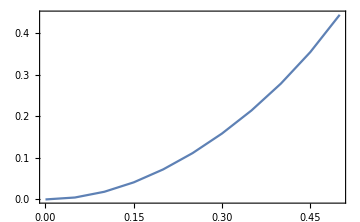

```mathematica
Block[ {δ={0.5,0.5}, r={1,0}, krange=50,range=3},DiscretePlot[ Abs[ProjIntSF[λ,δ,r,{2,1,2,1},krange,range]-ProjIntNN[λ,δ,r,{2,2,1,1},krange,range]]/ProjIntNN[λ,δ,r,{2,2,1,1},krange,range],{λ,0.,0.5,0.05},PlotLegends->Automatic]]
```

```mathematica
Block[ {λ=0.0,δ=0.5, r={1,0}, krange=50,range=3},DiscretePlot[ Abs[ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{1,0},{2,1,2,1},krange,range]-ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{0,1},{2,2,1,1},krange,range]]/ProjIntNN[λ,δ,r,{2,2,1,1},krange,range],{θ,0.,2π,0.1},PlotLegends->Automatic]]
```

$Aborted

```mathematica
Block[ {λ=0.2,δ=0.5, r={1,0}, krange=50,range=3},DiscretePlot[ Abs[ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{1,0},{2,1,2,1},krange,range]-ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{0,1},{2,2,1,1},krange,range]]/ProjIntNN[λ,δ,r,{2,2,1,1},krange,range],{θ,0.,2π,0.1},PlotLegends->Automatic]]
```